# Sperm and pollen competition drive sex chromosome turnover (do they?)

## Michael Scott & Matthew Osmond

This is much like van Doorn & Kirkpatrick 2007 (Nature 449:909), but with sperm/pollen competition as well (which we are hoping removes the need for sexually antagonistic selection to drive sex chromosome turnover).

## Resident life-cycle

We start with haploid selection, which occurs in sperm/pollen only. Let XAm be the frequency of allele A at the diallelic autosomal locus in gametes/pollen with an X allele at the diallelic sex-determining locus. Let YA be the frequency of allele A at the diallelic autosomal locus in gametes/pollen with an Y allele at the diallelic sex-determining locus. Let XAf be the frequency of allele A at the diallelic autosomal locus in eggs (which necessarily have an X allele at the diallelic sex-determining locus). After selection on male gametes/pollen we then have frequencies of A (and a) in each type of gamete/pollen:

```mathematica
wbarXm=wA XAm+wa Xam;
wbarY=wA YA+wa Ya;
XAms=wA*XAm/wbarXm;
Xams=wa*Xam/wbarXm;
YAs=wA*YA/wbarY;
Yas=wa*Ya/wbarY;
XAfs=XAf;
Xafs=Xaf;
```

Check that frequencies A and a in each gamete/pollen type sum to one after selection:

```mathematica
1==XAms+Xams//Factor
1==YAs+Yas//Factor
1==XAfs+Xafs/.XAf->1-Xaf
```

True

True

True

After random mating, the frequencies of the diploid genotypes in each sex are

```mathematica
XAXA=XAfs XAms;
XAXa=XAfs Xams+Xafs XAms ;
XaXa=Xafs Xams;
XAYA=XAfs YAs;
XAYa=XAfs Yas;
XaYA=Xafs YAs;
XaYa=Xafs Yas;
```

Check that frequencies of diploid genotypes in each sex sum to one after mating:

```mathematica
1==XAXA+XAXa+XaXa/.XAf->1-Xaf//Factor
1==XAYA+XAYa+XaYA+XaYa/.XAf->1-Xaf//Factor
```

True

True

After diploid selection (which can differ between males and females) the frequencies of the diploid genotypes in each sex are

```mathematica
wbarF=FAA XAXA+FAa XAXa+Faa XaXa;
wbarM=MAA XAYA+MAa XAYa+MAa XaYA+Maa XaYa;
XAXAs=FAA XAXA/wbarF;
XAXas=FAa XAXa/wbarF;
XaXas=Faa XaXa/wbarF;
XAYAs=MAA XAYA/wbarM;
XAYas=MAa XAYa/wbarM;
XaYAs=MAa XaYA/wbarM;
XaYas=Maa XaYa/wbarM;
```

Check that frequencies of diploid genotypes in each sex sum to one after diploid selection:

```mathematica
1==XAXAs+XAXas+XaXas//Factor
1==XAYAs+XAYas+XaYAs+XaYas//Factor
```

True

True

Finally, meiosis occurs, giving the haploid frequencies at the start of the next generation

```mathematica
XAfprime=XAXAs+XAXas/2;
Xafprime=XaXas+XAXas/2;
XAmprime=XAYAs+(1-r)XAYas+r XaYAs;
Xamprime=XaYas+r XAYas+(1-r) XaYAs;
YAprime=XAYAs+(1-r)XaYAs+ r XAYas;
Yaprime=XaYas+r XaYAs+(1- r) XAYas;
```

Check that frequencies of haploid genotypes sum to one after meiosis

```mathematica
1==XAfprime+Xafprime//Factor
1==XAmprime+Xamprime//Factor
1==YAprime+Yaprime//Factor
```

True

True

True

## Resident equilibrium

We now solve for the equilibrium frequency of A in each of the haploid genotypes. Equilibrium is achieved when the following three equations are zero

```mathematica
recursions={
XAfprime-XAf,
XAmprime-XAm,
YAprime-YA
};
```

To simplify the analysis we assume weak selection in both haploids (sperm/pollen) and diploids

```mathematica
weaksel={
MAA->1+sAm ϵ,
MAa->1+hAm sAm ϵ,
Maa->1,
FAA->1+sAf ϵ,
FAa->1+hAf sAf ϵ,
Faa->1,
wA->1+t ϵ,
wa->1
};
```

We can write the frequencies as Taylor series

```mathematica
frequenciessub={
XAf->XAf0+XAf1 ϵ,
XAm->XAm0+XAm1 ϵ,
YA->YA0+YA1 ϵ
};
```

Without selection the recursions for the change in frequency of A in each gamete/pollen type are

```mathematica
recursions0=Normal[Series[recursions/.weaksel/.Xaf->1-XAf/.Ya->1-YA/.Xam->1-XAm/.frequenciessub,{ϵ,0,0}]]
```

{1/2 (-XAf0+XAm0),XAf0-r XAf0-XAm0+r YA0,r XAf0-r YA0}

And at equilibrium we have

```mathematica
sol0=Solve[recursions0==0,{XAf0,XAm0}]
```

{{XAf0→YA0,XAm0→YA0}}

So, with no selection, the equilibrium frequency of A in each gamete/pollen type is equal (and we call this pA).

Now, looking at only the first order selection terms, the recursions for the change in frequency of A in each gamete/pollen type are

```mathematica
recursions1=Collect[Normal[Series[recursions/.weaksel/.Xaf->1-XAf/.Ya->1-YA/.Xam->1-XAm/.frequenciessub/.sol0/.YA0->pA,{ϵ,0,1}]],ϵ,Factor]//Flatten
```

{1/2 (2 hAf pA sAf+2 pA^2 sAf-6 hAf pA^2 sAf-2 pA^3 sAf+4 hAf pA^3 sAf+pA t-pA^2 t-XAf1+XAm1) ϵ,(hAm pA sAm+pA^2 sAm-3 hAm pA^2 sAm-pA^3 sAm+2 hAm pA^3 sAm+pA r t-pA^2 r t+XAf1-r XAf1-XAm1+r YA1) ϵ,(hAm pA sAm+pA^2 sAm-3 hAm pA^2 sAm-pA^3 sAm+2 hAm pA^3 sAm+pA t-pA^2 t-pA r t+pA^2 r t+r XAf1-r YA1) ϵ}

Instead of solving for the first order genotype frequencies we will instead solve for the difference in the frequency of A in the different gamete/pollen types.

The difference in the frequency of A with X in females and X in males is (at equilibrium to first order in selection)

```mathematica
eqdpAXfXm=Solve[recursions1[[1]]==0/.XAf1->dpAXfXm+XAm1,dpAXfXm]//Flatten
```

{dpAXfXm→2 hAf pA sAf+2 pA^2 sAf-6 hAf pA^2 sAf-2 pA^3 sAf+4 hAf pA^3 sAf+pA t-pA^2 t}

The difference in the frequency of A with X in males and Y is (at equilibrium to first order in selection)

```mathematica
eqdpAXmY=Solve[recursions1[[2]]==0/.XAf1->dpAXfXm+XAm1/.eqdpAXfXm/.XAm1->dpAXmY+YA1,dpAXmY]//Flatten
```

{dpAXmY→1/r(2 hAf pA sAf+2 pA^2 sAf-6 hAf pA^2 sAf-2 pA^3 sAf+4 hAf pA^3 sAf-2 hAf pA r sAf-2 pA^2 r sAf+6 hAf pA^2 r sAf+2 pA^3 r sAf-4 hAf pA^3 r sAf+hAm pA sAm+pA^2 sAm-3 hAm pA^2 sAm-pA^3 sAm+2 hAm pA^3 sAm+pA t-pA^2 t)}

The difference in the frequency of A with X in females and Y is (at equilibrium to first order in selection)

```mathematica
eqdpAXfY=Solve[recursions1[[3]]==0/.XAf1->dpAXfY+YA1,dpAXfY]//Flatten
```

{dpAXfY→(-hAm pA sAm-pA^2 sAm+3 hAm pA^2 sAm+pA^3 sAm-2 hAm pA^3 sAm-pA t+pA^2 t+pA r t-pA^2 r t)/r}

So then, to first order, the equilibrium haploid genotype frequencies are(?)

```mathematica
eqXAf=XAf0+ϵ dpAXfXm+ϵ dpAXmY/.sol0/.YA0->pA/.eqdpAXfXm/.eqdpAXmY//Simplify
```

{(pA ((-1+pA) (2 hAf (-1+2 pA) sAf-hAm sAm-pA (2 sAf+sAm-2 hAm sAm)-t) ϵ+r (1+t (ϵ-pA ϵ))))/r}

```mathematica
eqXAm=XAm0-ϵ dpAXfXm+ϵ dpAXfY/.sol0/.YA0->pA/.eqdpAXfXm/.eqdpAXfY//Simplify
```

{(pA (-(-1+pA) (-pA sAm+hAm (-1+2 pA) sAm-t) ϵ+r (1-2 pA sAf ϵ+2 pA^2 sAf ϵ-2 hAf (1-3 pA+2 pA^2) sAf ϵ)))/r}

```mathematica
eqYA=YA0-ϵ dpAXfY+ϵ dpAXfXm/.sol0/.YA0->pA/.eqdpAXfY/.eqdpAXfXm//Simplify
```

{(pA ((-1+pA) (-pA sAm+hAm (-1+2 pA) sAm-t) ϵ+r (1+2 pA sAf ϵ-2 pA^2 sAf ϵ+2 hAf (1-3 pA+2 pA^2) sAf ϵ)))/r}

The change in the equilibrium frequency of A is

```mathematica
dpA=Collect[Normal[Series[2 XAfprime+XAmprime+YAprime-(2XAf-XAm-YA)/.weaksel/.Xaf->1-XAf/.Ya->1-YA/.Xam->1-XAm/.XAf->eqXAf/.XAm->eqXAm/.YA->eqYA,{ϵ,0,1}]]/4,ϵ,Simplify]//Flatten
```

{pA+1/2 (-1+pA) pA (hAf (-1+2 pA) sAf-hAm sAm-pA (sAf+sAm-2 hAm sAm)-t) ϵ}

And at equilibrium we have

```mathematica
eqpA=Solve[dpA-pA==0,pA]//FullSimplify
```

{{pA→0},{pA→1},{pA→-(hAf sAf+hAm sAm+t)/(sAf-2 hAf sAf+sAm-2 hAm sAm)}}

Notice that when t=0 we have equation “avgpASubs” in van Doorn & Kirkpatrick 2007 (SOM page 6). Sperm/pollen selection acts to increase the frequency of A (if selected for, t>0).

Notice that, without sperm/pollen competition, the non-trivial equilibrium does not exist when there is no sexually antagonistic selection

```mathematica
Reduce[(0<pA/.eqpA[[3]]/.t->0)&&(1>pA/.eqpA[[3]]/.t->0)&&sAm>0&&sAf>0&&hAf>0&&hAm>0&&hAf<1&&hAm<1,Reals]
```

False

```mathematica
Reduce[(0<pA/.eqpA[[3]]/.t->0)&&(1>pA/.eqpA[[3]]/.t->0)&&sAm<0&&sAf<0&&hAf>0&&hAm>0&&hAf<1&&hAm<1,Reals]
```

False

But with sperm/pollen competition it can exist, even without sexually antagonistic selection

```mathematica
Reduce[(0<pA/.eqpA[[3]])&&(1>pA/.eqpA[[3]])&&sAm<0&&sAf<0&&hAf>0&&hAm>0&&hAf<1&&hAm<1&&t>0,Reals]
```

sAm<0&&((sAf≤sAm&&0<hAm<1&&((0<hAf<(sAf+sAm-2 hAm sAm)/(2 sAf)&&-hAf sAf-hAm sAm<t<-sAf+hAf sAf-sAm+hAm sAm)||((sAf+sAm-2 hAm sAm)/(2 sAf)<hAf<1&&-sAf+hAf sAf-sAm+hAm sAm<t<-hAf sAf-hAm sAm)))||(sAm<sAf<0&&((0<hAm≤(-sAf+sAm)/(2 sAm)&&0<hAf<1&&-hAf sAf-hAm sAm<t<-sAf+hAf sAf-sAm+hAm sAm)||((-sAf+sAm)/(2 sAm)<hAm<(sAf+sAm)/(2 sAm)&&((0<hAf<(sAf+sAm-2 hAm sAm)/(2 sAf)&&-hAf sAf-hAm sAm<t<-sAf+hAf sAf-sAm+hAm sAm)||((sAf+sAm-2 hAm sAm)/(2 sAf)<hAf<1&&-sAf+hAf sAf-sAm+hAm sAm<t<-hAf sAf-hAm sAm)))||((sAf+sAm)/(2 sAm)≤hAm<1&&0<hAf<1&&-sAf+hAf sAf-sAm+hAm sAm<t<-hAf sAf-hAm sAm))))

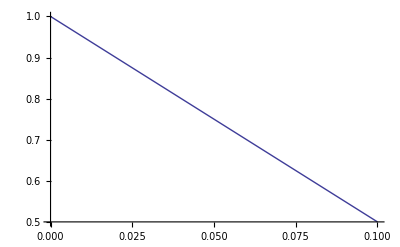

```mathematica
Plot[pA/.eqpA[[3]]/.sAf->-s/.sAm->-s/.hAf->h/.hAm->h/.s->1/10/.h->1,{t,0,1/10}]
```

## Invasion of a neo-Y

Now assume there is a rare mutation at a new locus y, which is a dominant (over the X) masculinizing factor. Let the frequency of this mutation be py.